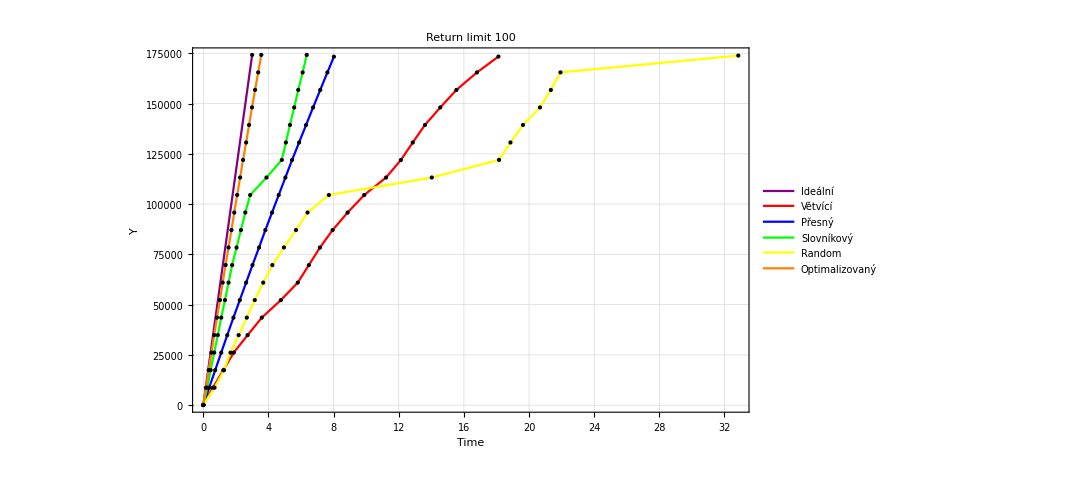

```mathematica
data0 ={
{0,100},
{3,174192}
};
data1={
{0, 100},
{0.59, 8711},
{1.23, 17411},
{1.87, 26183},
{2.72, 34836},
{3.59, 43541},
{4.76, 52250},
{5.8, 60961},
{6.48, 69673},
{7.16, 78382},
{7.94, 87090},
{8.86, 95801},
{9.88, 104507},
{11.22, 113217},
{12.13, 121927},
{12.86, 130636},
{13.61, 139350},
{14.55, 148061},
{15.54, 156765},
{16.8, 165477},
{18.12, 173348}
};

data2={
{0, 100},
{0.36, 8708},
{0.73, 17416},
{1.1, 26132},
{1.47, 34832},
{1.85, 43544},
{2.24, 52252},
{2.63, 60968},
{3.02, 69680},
{3.42, 78388},
{3.81, 87092},
{4.22, 95800},
{4.63, 104516},
{5.04, 113220},
{5.45, 121932},
{5.88, 130636},
{6.31, 139348},
{6.74, 148056},
{7.18, 156768},
{7.62, 165480},
{8.02, 173316}
};

data3={
{0, 100},
{0.24, 8708},
{0.45, 17453},
{0.67, 26172},
{0.89, 34882},
{1.1, 43555},
{1.33, 52268},
{1.55, 60980},
{1.77, 69673},
{2.04, 78392},
{2.31, 87088},
{2.58, 95824},
{2.88, 104524},
{3.88, 113222},
{4.82, 121960},
{5.07, 130638},
{5.32, 139367},
{5.58, 148055},
{5.83, 156804},
{6.1, 165484},
{6.35, 174192}
};

data4={
{0, 100},
{0.69, 8713},
{1.27, 17412},
{1.67, 26123},
{2.17, 34844},
{2.67, 43540},
{3.16, 52274},
{3.68, 60960},
{4.24, 69677},
{4.95, 78442},
{5.69, 87088},
{6.4, 95806},
{7.71, 104516},
{14.03, 113219},
{18.16, 121991},
{18.86, 130648},
{19.63, 139359},
{20.67, 148057},
{21.34, 156765},
{21.93, 165505},
{32.85, 173856}
};

data5={
{0, 100},
{0.16, 8702},
{0.33, 17444},
{0.5, 26128},
{0.67, 34859},
{0.84, 43561},
{1.02, 52301},
{1.19, 60966},
{1.37, 69708},
{1.55, 78414},
{1.73, 87097},
{1.9, 95797},
{2.08, 104538},
{2.26, 113228},
{2.44, 121971},
{2.63, 130640},
{2.81, 139393},
{2.99, 148094},
{3.18, 156816},
{3.37, 165489},
{3.56, 174192}
};

ListLinePlot[{data0,data1,data2,data3,data4,data5},AxesLabel->{"Time","Y"},PlotRange->All,PlotStyle->{Purple,Red,Blue,Green, Yellow, Orange},Mesh->All,MeshStyle->Directive[PointSize[Medium],Black],Frame->True,GridLines->Automatic,PlotLegends->{"Ideální","Větvící","Přesný","Slovníkový","Random","Optimalizovaný"},PlotLabel->"Return limit 100"]
```

```mathematica
data0 ={
{0,100},
{20,174192}
};
```

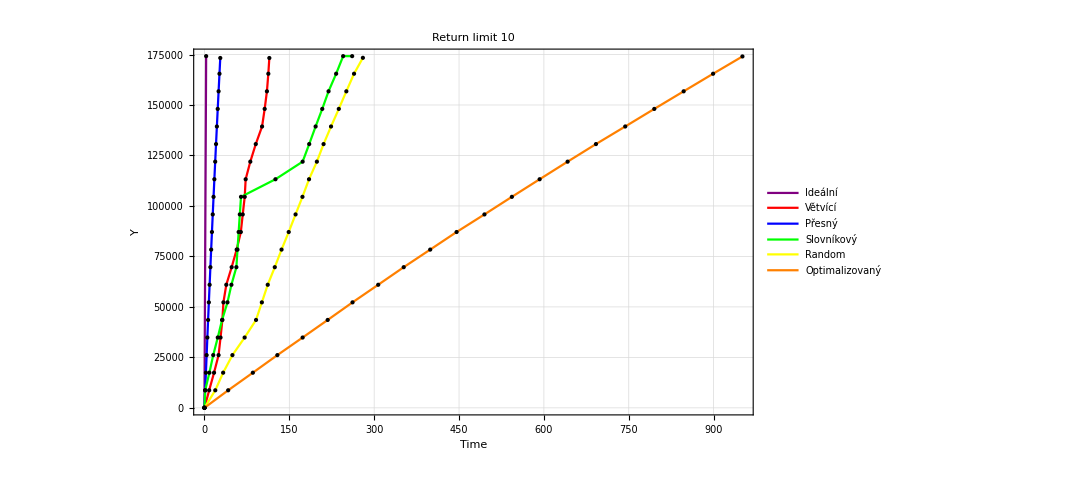

```mathematica
data1={
{0, 10},
{8.37, 8704},
{16.97, 17412},
{24.99, 26122},
{28.44, 34838},
{31.68, 43543},
{33.55, 52251},
{38.63, 60962},
{48.12, 69671},
{56.97, 78384},
{64.32, 87089},
{67.68, 95800},
{71.2, 104510},
{72.86, 113217},
{81.07, 121926},
{90.73, 130643},
{101.85, 139346},
{106.47, 148060},
{110.44, 156767},
{112.92, 165474},
{114.7, 173268}
};

data2={
{0, 10},
{1.28, 8708},
{2.58, 17420},
{3.88, 26122},
{5.16, 34830},
{6.45, 43542},
{7.8, 52256},
{9.16, 60966},
{10.51, 69670},
{11.88, 78378},
{13.27, 87094},
{14.68, 95804},
{16.1, 104508},
{17.54, 113218},
{19, 121930},
{20.49, 130640},
{21.98, 139352},
{23.49, 148056},
{25.02, 156766},
{26.58, 165476},
{27.98, 173280}
};

data3={
{0, 10},
{1.3, 8702},
{8.75, 17412},
{15.53, 26126},
{23.55, 34833},
{31.15, 43540},
{40.72, 52252},
{47.68, 60961},
{56.45, 69673},
{58.41, 78378},
{60.48, 87088},
{62.53, 95803},
{64.63, 104515},
{125.52, 113219},
{173.54, 121927},
{185.18, 130642},
{196.5, 139347},
{208.24, 148058},
{219.35, 156770},
{232.79, 165477},
{245.17, 174187},
{261.1, 174191}
};

data4={
{0, 10},
{19.17, 8706},
{33.07, 17417},
{49.45, 26122},
{71.03, 34831},
{91.21, 43542},
{101.48, 52249},
{111.87, 60967},
{124.33, 69669},
{136.29, 78386},
{148.96, 87088},
{161.06, 95798},
{173.23, 104507},
{184.85, 113220},
{198.72, 121926},
{210.56, 130636},
{223.76, 139347},
{237.49, 148061},
{250.82, 156765},
{264.42, 165474},
{280.06, 173362}
};

data5={
{0, 10},
{41.94, 8705},
{85.58, 17411},
{128.88, 26121},
{173.55, 34831},
{217.85, 43540},
{261.76, 52251},
{307.13, 60962},
{352.23, 69669},
{399.03, 78378},
{445.69, 87088},
{494.91, 95798},
{543.4, 104509},
{592.48, 113218},
{641.91, 121931},
{692.03, 130641},
{743.78, 139353},
{795.12, 148059},
{847.03, 156767},
{899.05, 165474},
{950.93, 174040}
};

ListLinePlot[{data0,data1,data2,data3,data4,data5},AxesLabel->{"Time","Y"},PlotRange->All,PlotStyle->{Purple,Red,Blue,Green, Yellow, Orange},Mesh->All,MeshStyle->Directive[PointSize[Medium],Black],Frame->True,GridLines->Automatic,PlotLegends->{"Ideální","Větvící","Přesný","Slovníkový","Random","Optimalizovaný"},PlotLabel->"Return limit 10"]
```

```mathematica
data0 ={
{0,100},
{6,174192}
};
```

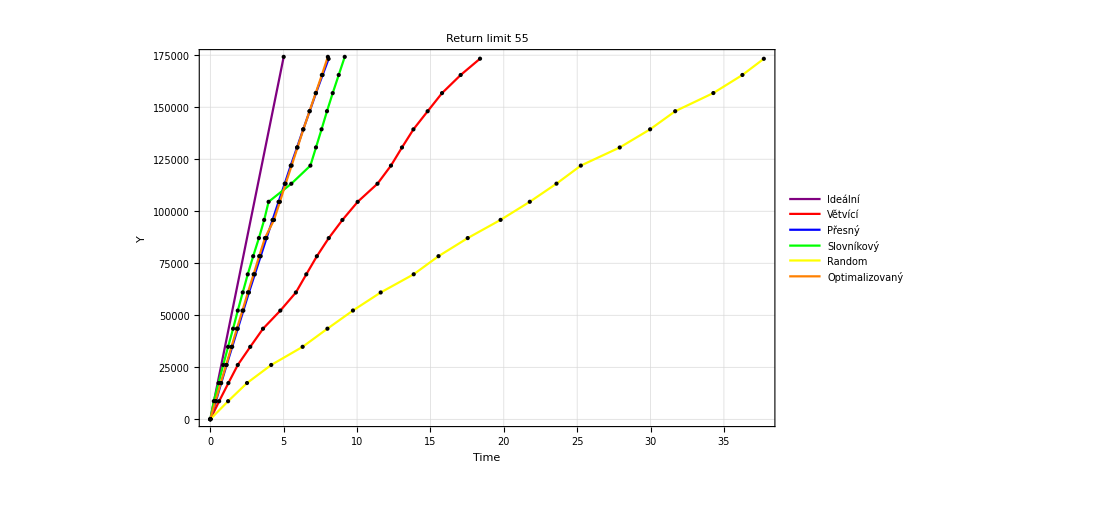

```mathematica
data1={
{0, 55},
{0.6, 8702},
{1.23, 17420},
{1.87, 26122},
{2.72, 34831},
{3.59, 43541},
{4.77, 52251},
{5.83, 60960},
{6.54, 69672},
{7.26, 78380},
{8.07, 87092},
{9, 95799},
{10.04, 104509},
{11.39, 113218},
{12.31, 121926},
{13.06, 130639},
{13.84, 139348},
{14.81, 148055},
{15.79, 156767},
{17.06, 165476},
{18.38, 173315}
};

data2={
{0, 55},
{0.38, 8707},
{0.74, 17414},
{1.11, 26126},
{1.49, 34838},
{1.87, 43550},
{2.25, 52250},
{2.63, 60967},
{3.03, 69674},
{3.43, 78386},
{3.83, 87098},
{4.24, 95798},
{4.65, 104510},
{5.07, 113222},
{5.48, 121927},
{5.91, 130639},
{6.33, 139346},
{6.77, 148063},
{7.2, 156775},
{7.65, 165482},
{8.06, 173229}
};

data3={
{0, 55},
{0.24, 8750},
{0.56, 17425},
{0.88, 26129},
{1.21, 34834},
{1.55, 43541},
{1.87, 52249},
{2.21, 60990},
{2.55, 69669},
{2.92, 78387},
{3.31, 87111},
{3.67, 95815},
{3.97, 104527},
{5.52, 113220},
{6.82, 121929},
{7.2, 130667},
{7.58, 139371},
{7.95, 148083},
{8.34, 156765},
{8.75, 165487},
{9.16, 174192}
};

data4={
{0, 55},
{1.21, 8703},
{2.5, 17438},
{4.15, 26125},
{6.29, 34844},
{7.98, 43560},
{9.72, 52288},
{11.61, 60959},
{13.86, 69705},
{15.55, 78398},
{17.54, 87101},
{19.78, 95845},
{21.77, 104542},
{23.59, 113254},
{25.25, 121933},
{27.9, 130639},
{29.97, 139369},
{31.68, 148062},
{34.28, 156800},
{36.26, 165484},
{37.72, 173272}
};

data5={
{0, 55},
{0.35, 8741},
{0.71, 17435},
{1.08, 26130},
{1.44, 34833},
{1.81, 43557},
{2.19, 52255},
{2.56, 60989},
{2.95, 69702},
{3.33, 78407},
{3.72, 87091},
{4.34, 95804},
{4.74, 104522},
{5.13, 113219},
{5.54, 121937},
{5.94, 130651},
{6.34, 139345},
{6.76, 148068},
{7.18, 156769},
{7.6, 165477},
{8.01, 174192}
};

ListLinePlot[{data0,data1,data2,data3,data4,data5},AxesLabel->{"Time","Y"},PlotRange->All,PlotStyle->{Purple,Red,Blue,Green, Yellow, Orange},Mesh->All,MeshStyle->Directive[PointSize[Medium],Black],Frame->True,GridLines->Automatic,PlotLegends->{"Ideální","Větvící","Přesný","Slovníkový","Random","Optimalizovaný"},PlotLabel->"Return limit 55"]
```